```mathematica
ClearAll["Global`*"];
If[Length[$FrontEnd]>0,SetDirectory[NotebookDirectory[]]];
Get["./DefinitionsAndAssumptions.m"];
ClearVars;
ShowVariableDefinitions
```

Definitions and assumptions for analysis of consumption and portfolio choice with risky and safe assets.

(r0 |  | log riskfree return (rate)
lℛ |  | log expected risky return factor (≠ 𝔼[Log[ℛtp1]])
σ |  | standard deviation of log risky return
ρ |  | relative risk aversion
φ |  | lℛ-r0 = log of the level equity premium (= Log[Φ]≠ 𝔼t[Log[Φtp1]])
ϛ |  | portfolio share in the risky asset)

Variables and formulas derived from the elemental environmental variables.

(R0 |  | Exp[r0] = riskfree return (factor)
ℛtp1 |  | Realized risky return (factor)
ℛ == 𝔼_t[ℛtp1] |  | Expected risky return (factor)
𝓇tp1 == Log[ℛtp1] |  | realized log risky return (rate)
𝓇tp1 | ~ | 𝒩(lℛ - σ^2/2,σ^2) → 𝔼_t[𝓇tp1] = lℛ - σ^2/2
𝓇 | = | 𝔼_t[𝓇tp1]
Φ |  | Expected equity premium (factor)
φ |  | lℛ-r0 = log of the level equity premium (= Log[Φ]≠ 𝔼t[Log[Φtp1]])
ϕtp1 |  | Realized logarithmic equity premium
ϕtp1 | ~ | 𝒩(φ - σ^2/2,σ^2) → {𝔼_t[ϕtp1] = φ - σ^2/2, log 𝔼Φtp1 = φ - σ^2/2 + σ^2/2 = φ} by MathFact LogELogNorm
ϕ  | = | 𝔼_t[ϕtp1] = Expectation of realized logarithmic equity premium
ℜtp1 | == | R0 + (ℛtp1-R0)ϛ  = arithmetic (exactly correct) portfolio return
ℜ | == | 𝔼_t[R0 + (ℛtp1-R0)ϛ] = expected arithmetic (exactly correct) portfolio return
lℜ | == | Log[ℜ] = arithmetic (exactly correct) portfolio return)

```mathematica
(*
Goal: Verify \eqref{eq:ERportToTheOneMinusRhoSimpler} in the LaTeX code 
*)
```

```mathematica
(* For some reason, the integration below does not work if σlℛ is used directly in the formula instead of σ; 
so integration is done with σ and then σ is replaced with σlℛ in the result *)
𝔼tℜtp1ToTheOneMinusRho = Integrate[ℜ^(1-ρ) PDF[LogNormalDistribution[(lℛ-σ^2/2),σ],ℜ],{ℜ,0,∞}] /. σ -> σlℛ
```

ⅇ^(1/2 (-1+ρ) (-2 lℛ+ρ σlℛ^2))

```mathematica
Log𝔼tℜtp1ToTheOneMinusRho =𝔼tℜtp1ToTheOneMinusRho[[2]] (* For some reason, just taking the Log does not extract the exponent ... *)
```

1/2 (-1+ρ) (-2 lℛ+ρ σlℛ^2)

```mathematica
(* Verify that Mathematica's answer is equivalent to the answer in CRRA-RateRisk.tex: \eqref{eq:ERportToTheOneMinusRho} *)
(* Two expressions are equal if the difference between them is zero *)
```

```mathematica
{Simplify[Log𝔼tℜtp1ToTheOneMinusRho-(1-ρ)(lℛ - ρ σlℛ^2/2)]
,Simplify[Log𝔼tℜtp1ToTheOneMinusRho-(1-ρ)(lℛ - ρ σlℛ^2/2 + σlℛ^2/2-σlℛ^2/2)]
,Simplify[Log𝔼tℜtp1ToTheOneMinusRho-(1-ρ)(lℛ + (1-ρ )σlℛ^2/2 -σlℛ^2/2)]
,Simplify[Log𝔼tℜtp1ToTheOneMinusRho-(1-ρ)(lℛ -σlℛ^2/2+ (1-ρ )σlℛ^2/2 )]
,Simplify[Log𝔼tℜtp1ToTheOneMinusRho-(1-ρ)(lℛ -σlℛ^2/2)- (1-ρ )^2 σlℛ^2/2 ]
,Simplify[Log𝔼tℜtp1ToTheOneMinusRho-(1-ρ)(lℛ -σlℛ^2/2)- (1-ρ )^2 σlℛ^2/2 ]
}
```

{0,0,0,0,0,0}

```mathematica
(* Verify \eqref{eq:ERportToTheOneMinusRhoSimpler} *)
```

```mathematica
{Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-2ρ + ρ^2)σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ+(1-ρ)(-σlℛ^2/2)+(1-2ρ + ρ^2)σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ-(1-ρ)(σlℛ^2/2)+(1-2ρ + ρ^2)σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ-(1)(σlℛ^2/2)+(+ρ)(σlℛ^2/2)+(1-2ρ + ρ^2)σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ-(1)(σlℛ^2/2)+(+ρ)(σlℛ^2/2)+(-2ρ )σlℛ^2/2+(1+ ρ^2)σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ+ρ(σlℛ^2/2)-ρ σlℛ^2+ ρ^2 σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ+ρ((σlℛ^2/2)- σlℛ^2)+ ρ^2 σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ+ρ σlℛ^2((1/2)- 1)+ ρ^2 σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ-ρ σlℛ^2/2+ ρ^2 σlℛ^2/2]
,Simplify[(1-ρ)(lℛ-σlℛ^2/2)+(1-ρ)^2 σlℛ^2/2]==Simplify[(1-ρ)lℛ-ρ (1-ρ)σlℛ^2/2]
}
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Use the result just derived *)
𝔼ℜPart = Exp[(1-ρ)lℛ-ρ (1-ρ)σlℛ^2/2]
```

ⅇ^(lℛ (1-ρ)-1/2 (1-ρ) ρ σlℛ^2)

```mathematica
(* Exact formula for the MPC \eqref{eq:MPCExact} *)
κ = 1-(β 𝔼ℜPart)^(1/ρ)
```

1-(ⅇ^(lℛ (1-ρ)-1/2 (1-ρ) ρ σlℛ^2) β)^(1/ρ)

```mathematica
(* Derivative of the MPC with respect to the standard deviation of the risky shock *)
dκdσlℛ = D[κ,σlℛ]
```

ⅇ^(lℛ (1-ρ)-1/2 (1-ρ) ρ σlℛ^2) β (ⅇ^(lℛ (1-ρ)-1/2 (1-ρ) ρ σlℛ^2) β)^(-1+1/ρ) (1-ρ) σlℛ

```mathematica
𝔼ℜPartToTheOneMinusRho = Exp[(ρ^-1-1)lℛ-(1-ρ)σlℛ^2/2]
```

ⅇ^(lℛ (-1+1/ρ)-1/2 (1-ρ) σlℛ^2)

```mathematica
𝔼ℜPartToTheOneMinusRhoApprox=(1+(ρ^-1-1)lℛ-(1-ρ)σlℛ^2/2)
```

1+lℛ (-1+1/ρ)-1/2 (1-ρ) σlℛ^2

```mathematica
βPartApprox = 1-ϑ ρ^-1
```

1-ϑ/ρ

```mathematica
κApprox = 1-βPartApprox 𝔼ℜPartToTheOneMinusRhoApprox
```

1-(1-ϑ/ρ) (1+lℛ (-1+1/ρ)-1/2 (1-ρ) σlℛ^2)

```mathematica
κApproxApprox = 1-(1-ϑ ρ^-1+(ρ^-1-1)lℛ-(1-ρ)σlℛ^2/2)
```

-lℛ (-1+1/ρ)+ϑ/ρ+1/2 (1-ρ) σlℛ^2

```mathematica
{Simplify[κApprox-κApproxApprox]}(* Verifies that the terms left out are small numbers multiplied by small numbers *)
```

{(ϑ (-1+ρ) (-2 lℛ+ρ σlℛ^2))/(2 ρ^2)}

```mathematica
(* Verify \eqref{eq:MPCApprox} *)
{Simplify[κApproxApprox]==Simplify[ 1-(1-ϑ ρ^-1+(ρ^-1-1)lℛ-(1-ρ)σlℛ^2/2)]
,Simplify[κApproxApprox]==Simplify[ -(-ϑ ρ^-1+(ρ^-1-1)lℛ-(1-ρ)σlℛ^2/2)]
,Simplify[κApproxApprox]==Simplify[ (ϑ ρ^-1-(ρ^-1-1)lℛ+(1-ρ)σlℛ^2/2)]
,Simplify[κApproxApprox]==Simplify[ (ϑ ρ^-1+(1-ρ^-1)lℛ+(1-ρ)σlℛ^2/2)]
,Simplify[κApproxApprox- (ϑ ρ^-1+(lℛ-lℛ  ρ^-1)+(1-ρ)σlℛ^2/2)]
,Simplify[κApproxApprox- ((ϑ-lℛ) ρ^-1+lℛ+(1-ρ)σlℛ^2/2)]
,Simplify[κApproxApprox- (lℛ- ρ^-1(lℛ-ϑ)-(ρ-1)σlℛ^2/2)]
}
```

{True,True,True,True,0,0,0}

```mathematica
dκApproxApproxdσlℛ = D[(lℛ- ρ^-1(lℛ-ϑ)-(ρ-1)σlℛ^2/2),σlℛ]
```

-(-1+ρ) σlℛ

```mathematica
Simplify[dκApproxApproxdσlℛ - (-(ρ-1) σlℛ)] (* Verify that expression involving σlℛ in the handout is right *)
```

0

```mathematica
dκApproxApproxdσlℛ = -(ρ-1)  σlℛ;
```

```mathematica
κApproxApprox
```

-lℛ (-1+1/ρ)+ϑ/ρ+1/2 (1-ρ) σlℛ^2

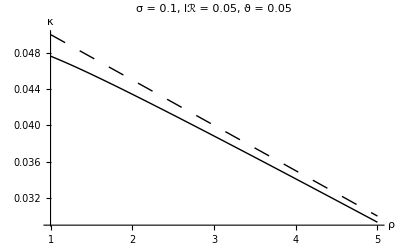

```mathematica
σlℛ=0.1;lℛ=0.05;ϑ=0.05;β=1/(1+ϑ);
Needs["PlotLegends`"];
MPCvsCRRA = Plot[{κ,κApproxApprox},{ρ,1,5}
,PlotStyle->{
{Black,Thick}
,{Black,Dashing[{0.03}]}
,{Black,Dashing[{0.005,0.01}]}}
,AxesLabel->{"ρ","κ"}
,PlotLabel->"σ = "<>ToString[σlℛ]<>", lℛ = "<>ToString[lℛ]<>", ϑ = "<>ToString[ϑ]
,PlotLegend->{Text[Style["True",FontSize->14]],Text[Style["Approx",FontSize->14]]}
,LegendSize->0.5
,LegendPosition->{.25,0.}
,BaseStyle->{FontSize->14}
];
Export["../../Figures/MPCvsCRRA.pdf",MPCvsCRRA];
Export["../../Figures/MPCvsCRRA.png",MPCvsCRRA,ImageSize->72 9];
Export["../../Figures/MPCvsCRRA.svg",MPCvsCRRA];
Print[MPCvsCRRA];
```

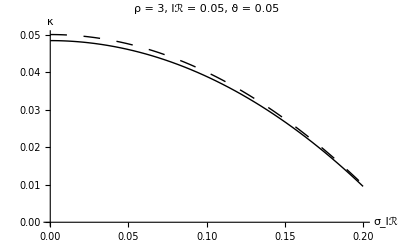

```mathematica
lℛ=0.05;ϑ=0.05;β=1/(1+ϑ);ρ=3;
Needs["PlotLegends`"];
MPCvsSigma = Plot[{κ,κApproxApprox},{σlℛ,0.,0.2}
,PlotStyle->{
{Black,Thick}
,{Black,Dashing[{0.03}]}
,{Black,Dashing[{0.005,0.01}]}}
,AxesLabel->{"σ_lℛ","κ"}
,PlotLabel->"ρ = "<>ToString[ρ]<>", lℛ = "<>ToString[lℛ]<>", ϑ = "<>ToString[ϑ]
,PlotLegend->{Text[Style["True",FontSize->14]],Text[Style["Approx",FontSize->14]]}
,LegendSize->0.5
,LegendPosition->{.25,0.}
,BaseStyle->{FontSize->14}
,PlotRange->{Automatic,{0.,Automatic}}
];
Export["../../Figures/MPCvsSigma.pdf",MPCvsSigma];
Export["../../Figures/MPCvsSigma.png",MPCvsSigma,ImageSize->72 9];
Export["../../Figures/MPCvsSigma.svg",MPCvsSigma];
Print[MPCvsSigma];
```